```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WEFF.xlsx"]
```

```mathematica
data1={{10.,80.83612040133778},{11.,78.10329205678043},{12.,76.54015401540154},{12.9,75.5877493963655},{14.5,71.98835647111508},{16.,70.02016129032258},{17.5,67.49084249084248},{19.,65.82299698290312},{20.9,63.62425049966689},{22.9,61.02551426766637},{25.,58.92834890965732},{27.,56.664380429812525},{29.,54.62238206050349},{31.,52.822580645161295},{33.,50.964187327823694},{34.,49.90255138199858},{35.,48.940368940368934},{37.,47.59983864461477},{39.,46.5483234714004},{40.,46.747787610619476}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\BEFF.xlsx"]
```

```mathematica
data2={{10.,16.16161616161616},{11.,15.497254423428922},{12.,15.083333333333332},{13.,14.796831075900842},{14.,14.285714285714286},{15.,14.015401540154016},{16.5,13.611525086934924},{18.,13.108206245461146},{20.,12.532467532467532},{22.,12.140762463343108},{24.,11.672008547008547},{25.4,11.447414614574454},{27.,11.099278191929947},{28.4,10.887547507265817},{30.,10.557308096740275},{31.5,10.3424178895877},{32.9,10.141270478484447},{34.,9.994468006638392}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\GEFF.xlsx"]
```

```mathematica
data3={{10.,68.01916932907348},{11.4,64.99582289055974},{12.9,62.35786075856503},{15.,58.24999999999999},{16.5,56.52789578023223},{17.9,54.54734723619834},{19.5,52.54827477049699},{21.,50.827838827838825},{22.5,49.638718473074306},{24.,48.50460122699387},{25.4,47.74822354522758},{27.,46.17809298660362},{28.4,45.166453265044815},{30.,44.01010101010102},{32.,42.46987951807228},{34.,41.396618527650574},{35.9,39.884268470619446},{37.9,38.40341990087925},{40.,37.41176470588235}};
```

```mathematica
a1=ListPlot[data1];
```

```mathematica
b1=ListPlot[data2];
```

```mathematica
c1=ListPlot[data3];
```

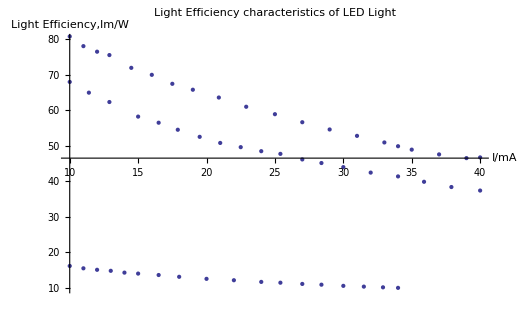

```mathematica
Show[a1,b1,c1,AxesLabel->{"I/mA","Light Efficiency,lm/W"},PlotLabel->"Light Efficiency characteristics of LED Light",PlotRange->{10,80}]
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WUEFF.xlsx"]
```

```mathematica
data4={{200.,1.9090909090909094},{209.9,2.65774957227311},{220.,3.555844155844156},{229.9,6.887052341597796},{240.,5.767857142857143},{245.,6.360698125404008},{250.,6.989565217391305}};
```

```mathematica
data4={{200.,1.9090909090909094},{209.9,2.65774957227311},{220.,3.555844155844156},{229.9,6.887052341597796},{240.,5.767857142857143},{245.,6.111801242236025},{250.,7.27420814479638}};
```

```mathematica
d1=ListPlot[data4];
```

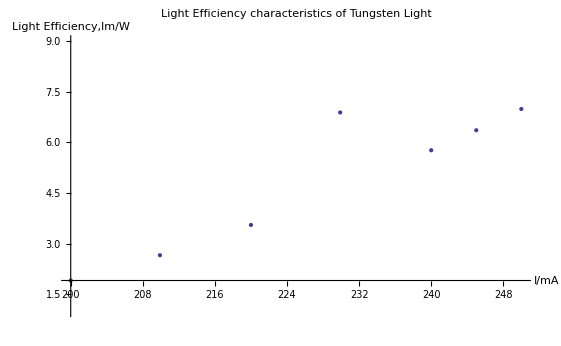

```mathematica
Show[d1,AxesLabel->{"I/mA","Light Efficiency,lm/W"},PlotLabel->"Light Efficiency characteristics of Tungsten Light",PlotRange->{1,9}]
```